# Midterm 2

## Question 1

```mathematica
Ual=(3/4)*Log[200-x+16]+(1/4)*Log[200-x]
Uan=Log[200]
```

1/4 Log[200-x]+3/4 Log[216-x]

Log[200]

NSolve[0.25 Log[200-x]+0.75 Log[216-x]==5.29832,x]

```mathematica
f[x_]:=Ual-Uan
```

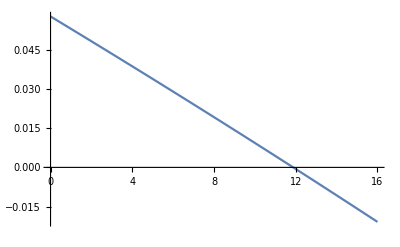

```mathematica
Plot[f[x],{x,0,16}]
```

```mathematica
NSolve[f[x]==0]
```

{{x→11.8767}}

```mathematica
Ubl=(3/4)*Sqrt[200-x+16]+(1/4)*Sqrt[200-x]
Ubn=Sqrt[200]
```

(√(200-x))/4+(3 √(216-x))/4

10 √2

```mathematica
NSolve[Ubl==Ubn]
```

{{x→11.9388}}

```mathematica
Exit[]
```

## Question 2

```mathematica
f=x+Log[y]/2+Sqrt[z]/4
L=f-λ1*(x+y+z-20)-λ2*(x-4)
```

x+(√z)/4+Log[y]/2

x+(√z)/4-(-20+x+y+z) λ1-(-4+x) λ2+Log[y]/2

Practice: Do cases 1 and 3....

### Case 1 : λ1 = 0 and λ2 = 0 Case 3 : λ1 >0 and λ2 = 0

### Case 2: λ1=0 and λ2>0

```mathematica
FOC=Thread[Grad[L,{x,y,z,λ2}]==0]
```

{1-λ1-λ2==0,1/(2 y)-λ1==0,1/(8 √z)-λ1==0,4-x==0}

```mathematica
sys=Join[FOC,{λ1==0}]
```

{1-λ1-λ2==0,1/(2 y)-λ1==0,1/(8 √z)-λ1==0,4-x==0,λ1==0}

```mathematica
Solve[sys,{x,y,z,λ1,λ2}]
```

{}

There is no solution so this case is inconsistent.

### Case 4 : λ1 > 0 and λ2 > 0

```mathematica
sys=Thread[Grad[L,{x,y,z,λ1,λ2}]==0]
```

{1-λ1-λ2==0,1/(2 y)-λ1==0,1/(8 √z)-λ1==0,20-x-y-z==0,4-x==0}

```mathematica
sol=Solve[sys,{x,y,z,λ1,λ2}][[1]]
```

{x→4,y→8 (-1+√5),z→8 (3-√5),λ1→1/64 (1+√5),λ2→1/64 (63-√5)}

```mathematica
N[sol]
```

{x→4.,y→9.88854,z→6.11146,λ1→0.0505636,λ2→0.949436}

This case is consistent with a solution.

## Question 3

```mathematica
Exit[]
```

```mathematica
u:=Sqrt
δ=4/5;
U[c0_,c1_]:=u[c0]+δ*u[c1]
```

```mathematica
prices={p0,p1}
basket={c0,c1}
endowment ={10,20}
```

{p0,p1}

{c0,c1}

{10,20}

#### 3.1

```mathematica
budget= prices.basket == prices.endowment (* income is the value of the endowment!*)
```

c0 p0+c1 p1==10 p0+20 p1

#### 3.2

Since this is a pure trade economy (no production). The supply of c0 is just the aggregate endowment of c0 and since Eva is the ONLY consumer in this economy, the aggregate endowment coincides with her endowment: 10

```mathematica
c0Supply=10
```

10

#### 3.3

Solving Eva’s utility max. problem to obtain her demands:

```mathematica
budget
budget[[1]]
budget[[2]]
L=U[c0,c1]-λ*(budget[[1]]-budget[[2]])
```

c0 p0+c1 p1==10 p0+20 p1

c0 p0+c1 p1

10 p0+20 p1

√c0+(4 √c1)/5-(-10 p0+c0 p0-20 p1+c1 p1) λ

```mathematica
vars={c0,c1,λ}
gradient=Grad[L,vars]
FOC=Thread[gradient==0]
solution=Solve[FOC,vars][[2]]
c0Demand= c0/.solution
```

{c0,c1,λ}

{1/(2 √c0)-p0 λ,2/(5 √c1)-p1 λ,10 p0-c0 p0+20 p1-c1 p1}

{1/(2 √c0)-p0 λ==0,2/(5 √c1)-p1 λ==0,10 p0-c0 p0+20 p1-c1 p1==0}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{c0→(250 (p0 p1+2 p1^2))/(p0 (16 p0+25 p1)),c1→(160 (p0^2+2 p0 p1))/(p1 (16 p0+25 p1)),λ→(√(16 p0+25 p1))/(√p0 √p1 √(1000 p0+2000 p1))}

(250 (p0 p1+2 p1^2))/(p0 (16 p0+25 p1))

```mathematica
marketclear=c0Supply==c0Demand /. p0->1
```

10==(250 (p1+2 p1^2))/(16+25 p1)

```mathematica
Solve[marketclear,p1]
```

{{p1→-(2 √2)/5},{p1→(2 √2)/5}}

We chose the second solution since p1 < 0 does not make economic sense.

```mathematica
p1=(2* √2.0)/5
```

0.565685

## Question 4

## -Graphics-

```mathematica
Exit[]
```

#### 4.1

```mathematica
budget={c0+z==e0,c1==e1+z*r}/.{e0->10,e1->20}
budget[[1,1]]
budget[[1,2]]
budget[[2,1]]
budget[[2,2]]
```

{c0+z==10,c1==20+r z}

c0+z

10

c1

20+r z

```mathematica
u[c_]:=Sqrt[c]
δ=4/5
```

4/5

```mathematica
budget
```

{c0+z==10,c1==20+r z}

```mathematica
U[c0_,c1_]:=u[c0]+δ*u[c1]
(* U=u[c0]+δ*u[c1] lazy notation, works for ALL MOST ALL problems *)
```

We re-write the utility (using the budget constraints) as a function of the portfolio (in this case, the amount invested in the bond, z):

```mathematica
Uz=U[10-z,20+r*z]
```

√(10-z)+4/5 √(20+r z)

To maximize utility:

```mathematica
D[Uz,z]==0
```

-1/(2 √(10-z))+(2 r)/(5 √(20+r z))==0

The bond demand is the amount of z that maximizes the utility:

```mathematica
sol=Solve[D[Uz,z]==0,z][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{z→(20 (-25+8 r^2))/(r (25+16 r))}

In equilibrium, returns must be such that the net holdings of any financial asset are zero (remember that if the agent sells/supplies a financial asset he/she holds a negative dollar amount of the asset so the dollar amount sold plus the dollar amount bought add up to zero in equilibrium).

```mathematica
Solve[(20 (-25+8 r^2))/(r (25+16 r))==0]
```

{{r→-5/(2 √2)},{r→5/(2 √2)}}

```mathematica
equation=x+y== 200+z
equation[[1]]
equation[[2]]
```

x+y==200+z

x+y

200+z

## Question 5

Yes there is an arbitrage opportunity. For example, the portfolio, wA=+1, wB=+3, wC=-1 generates a payoff of $0 in t=0, $0 in t=1, and $1 in t=2.

Asset C.

Assets A and B.

(non-negative)   (positive)

```mathematica
rA={-1,3,0}
rB={0,-1,2}
rC={-1,0,5}
```

{-1,3,0}

{0,-1,2}

{-1,0,5}

```mathematica
Total[{1,3,-1}*{rA,rB,rC}]
```

{0,0,1}